```mathematica
Quit[]
```

## Load Packages

```mathematica
$LoadFeynArts=True;
Global`$LoadAddOns={"FeynHelpers"};
<<FeynCalc`;
$FAVerbose = 0;

FAPatch[PatchModelsOnly->True];
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

FeynArts 3.1 patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

FeynHelpers 1.1.0 loaded.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

Patching FeynArts models... done!

## Diagram and amplitude utilities

### Functions for generating diagrams

```mathematica
(*exclusions=Join[{V[1],V[2],V[3],V[4]},mesonList];*)
exclusions={V[1],V[2],V[3](*,V[4]*)};

frModelName="EFT_MeV_DM_vector_no_contact";
model={frModelName<>"/"<>frModelName};
genericModel={"Lorentz",frModelName<>"/"<>frModelName};

insertionLevel={Particles};
```

```mathematica
genDiags[inFields_,outFields_,nLoops_:0,adj_:{3,4,5},otherExclusions_:{}]:=Block[{tops},
tops=CreateTopologies[nLoops, Length[inFields]-> Length[outFields],ExcludeTopologies-> {Tadpoles,SelfEnergies,WFCorrections},Adjacencies-> adj];
InsertFields[tops,inFields-> outFields,InsertionLevel-> insertionLevel,Model-> model,GenericModel-> genericModel,ExcludeParticles-> Join[exclusions,otherExclusions]]
]
```

### Abbreviations for states

```mathematica
stateπ0=S[1];
stateπm=S[2];
stateπp=-S[2];
statek0=S[3];
statek0bar=-S[3];
statekm=S[4];
statekp=-S[4];
stateη=S[5];
stateγ=V[1];
stateρ=V[2];
stateω=V[3];
statev=V[4];
stateν=F[1];
stateνbar=-F[1];
statel=F[2];
statelbar=-F[2];
statex=F[3];
statexbar=-F[3];

mesonList={stateπ0,stateπp,stateπm,statekp,statekm,statek0,statek0bar,stateη};
```

### Three body phase space bounds

```mathematica
getTBounds[s_,m1_,m2_,m3_,M_]:=Module[{E1,E2,t,BoundsLHS,BoundsRHS,solns,holdassumptions},
holdassumptions=$Assumptions;
$Assumptions=Join[$Assumptions,{getSBounds⟦1⟧<s<getSBounds⟦2⟧}];
(* energies *)
E1=  (M^2+m1^2-s)/(2M);
E2= (M^2+m2^2-t)/(2M);
(* LHS boundary equation *)
BoundsLHS=(M^2+2E1 E2 +m1^2+m2^2-m3^2-2M(E1+E2))//Simplify;
(* RHS boundary equation *)
BoundsRHS=(2 √((E1^2-m1^2)(E2^2-m2^2)))//FullSimplify;
(* solution to boundary equation *)
solns=Simplify[Solve[BoundsLHS==BoundsRHS,t]];
$Assumptions=holdassumptions;
{solns⟦2⟧⟦1⟧⟦2⟧,solns⟦1⟧⟦1⟧⟦2⟧}
]

getSBounds[m1_,m2_,m3_,M_]:={(m2+m3)^2,(M-m1)^2};


getYBounds[x_,m1_,m2_,m3_,M_]:=Module[{E1,E2,y,BoundsLHS,BoundsRHS,solns,holdassumptions},
holdassumptions=$Assumptions;
$Assumptions=Join[$Assumptions,{getXBounds⟦1⟧<x<getXBounds⟦2⟧}];
(* energies *)
E1=  M x/ 2;
E2= M y/ 2;
(* LHS boundary equation *)
BoundsLHS=(M^2+2E1 E2 +m1^2+m2^2-m3^2-2M(E1+E2))//Simplify;
(* RHS boundary equation *)
BoundsRHS=(2 √((E1^2-m1^2)(E2^2-m2^2)))//FullSimplify;
(* solution to boundary equation *)
solns=Simplify[Solve[BoundsLHS==BoundsRHS,y]];
$Assumptions=holdassumptions;
{solns⟦2⟧⟦1⟧⟦2⟧,solns⟦1⟧⟦1⟧⟦2⟧}]


getXBounds[m1_,m2_,m3_,M_]:={(M^2-(M-m1)^2+m1^2)/M^2,(M^2-(m2+m3)^2+m1^2)/M^2};
```

## V→ l̄ l

### Compute Matrix Element

```mathematica
ClearScalarProducts[]
```

Null[]

```mathematica
SP[pl,pl]=(μl*mv)^2;
SP[plbar,plbar]=(μl*mv)^2;
SP[k,k]=0;
SP[pv,pv]=mv^2;

SP[pl,plbar]=1/2(mv^2-(μl*mv)^2-(μl*mv)^2);
```

```mathematica
Module[{diags,ampFA,ampFC,amp,ampConj,msqrd},
diags=genDiags[{statev},{statel,statelbar}];

ampFA=CreateFeynAmp[diags];

ampFC=FCFAConvert[ampFA,
IncomingMomenta-> {pv},
OutgoingMomenta-> {pl,plbar},
List-> False,
UndoChiralSplittings-> True,
LorentzIndexNames-> {μ,ν,ρ,σ},
ChangeDimension-> 4,
FinalSubstitutions-> M$FACouplings];

amp=ampFC//PropagatorDenominatorExplicit//Contract//ReplaceAll[#,ml-> μl*mv]&;
ampConj=ComplexConjugate[amp]//ReplaceAll[#,{μ-> α,ν-> β,ρ-> λ,σ-> ζ}]&;
msqrd = amp*ampConj//FermionSpinSum//ReplaceAll[#,DiracTrace-> Tr]&//DoPolarizationSums[#,pv]&;
msqrd = msqrd//ReplaceAll[#,pv-> pl+plbar]&//ExpandScalarProduct//Simplify;
vllbar`msqrd=msqrd
]
```

4 gvll^2 (2 μl^2+1) mv^2

```mathematica
vllbar`Γ=1/(2mv)(4π)/(16 π^2)((√(1-4 μl^2))/2)vllbar`msqrd//FullSimplify
```

(gvll^2 √(1-4 μl^2) (2 μl^2+1) mv)/(4 π)

## V→ l̄ l γ

### Compute Matrix element

```mathematica
ClearScalarProducts[]
```

Null[]

```mathematica
SP[pl,pl]=(μl*mv)^2;
SP[plbar,plbar]=(μl*mv)^2;
SP[k,k]=0;
SP[pv,pv]=mv^2;

SP[pl,plbar]=1/2(s-(μl*mv)^2-(μl*mv)^2);
SP[k,plbar]=1/2(t-0-(μl*mv)^2);
SP[k,pl]=1/2(u-0-(μl*mv)^2);
```

```mathematica
Module[{diags,ampFA,ampFC,amp,ampConj,msqrd},
diags=genDiags[{statev},{statel,statelbar,stateγ}];

ampFA=CreateFeynAmp[diags];

ampFC=FCFAConvert[ampFA,
IncomingMomenta-> {pv},
OutgoingMomenta-> {pl,plbar,k},
List-> False,
UndoChiralSplittings-> True,
LorentzIndexNames-> {μ,ν,ρ,σ},
ChangeDimension-> 4,
FinalSubstitutions-> M$FACouplings];

amp=ampFC//PropagatorDenominatorExplicit//Contract//ReplaceAll[#,ml-> μl*mv]&;
ampConj=ComplexConjugate[amp]//ReplaceAll[#,{μ-> α,ν-> β,ρ-> λ,σ-> ζ}]&;
msqrd = amp*ampConj//FermionSpinSum//ReplaceAll[#,DiracTrace-> Tr]&;
msqrd = msqrd//DoPolarizationSums[#,k,0]&//DoPolarizationSums[#,pv]&//Simplify;
msqrd=msqrd//ReplaceAll[#,pv-> pl+plbar+k]&//ScalarProductExpand//MomentumExpand//ExpandScalarProduct//Simplify;
vllbarγ`msqrd=msqrd]
```

-1/(mv^2 (t-μl^2 mv^2)^2 (u-μl^2 mv^2)^2)4 gvll^2 qe^2 (2 μl^8 (18 μl^2+7) mv^10-2 μl^6 mv^8 ((21 μl^2-2) s+(37 μl^2+2) (t+u))+μl^4 mv^6 (2 (8 μl^2-1) s^2+2 (34 μl^2-3) s (t+u)+(58 μl^2-7) (t+u)^2)+μl^2 mv^4 (-2 μl^2 s^3-2 (10 μl^2-1) s^2 (t+u)+s ((4-37 μl^2) t^2+(4-82 μl^2) t u+(4-37 μl^2) u^2)-3 (7 μl^2-1) (t+u)^3)+mv^2 (2 μl^2 s^3 (t+u)+s^2 (6 μl^2 t^2+2 (10 μl^2-1) t u+6 μl^2 u^2)+s (t+u) (7 μl^2 t^2+2 (11 μl^2-1) t u+7 μl^2 u^2)+3 μl^2 t^4+(14 μl^2-1) t^3 u+18 μl^2 t^2 u^2+(14 μl^2-1) t u^3+3 μl^2 u^4)-t u (2 s^3+4 s^2 (t+u)+s (3 t^2+4 t u+3 u^2)+t^3+t^2 u+t u^2+u^3))

### Convert to x and y

```mathematica
vllbarγ`dΓdsdt=(1/(2mv))(1/(16 mv^2(2π)^3))vllbarγ`msqrd//ReplaceAll[#,u-> mv^2+2 mv^2 μl^2-s-t]&//Simplify;
vllbarγ`dΓdxdy=mv^4 vllbarγ`dΓdsdt//ReplaceAll[#,{s-> mv^2(1-x),t-> mv^2(1-y+μl^2)}]&//Simplify;
```

```mathematica
vllbarγ`dΓdxdy`dynamic=vllbarγ`dΓdxdy//SelectNotFree[#,y]&;
vllbarγ`dΓdxdy`coeff=vllbarγ`dΓdxdy//SelectFree[#,y]&;
```

```mathematica
vllbarγ`dΓdxdy`dynamic*vllbarγ`dΓdxdy`coeff-vllbarγ`dΓdxdy
```

0

```mathematica
vllbarγ`dΓdxdy`coeff
```

-(gvll^2 mv qe^2)/(32 π^3)

```mathematica
vllbarγ`dΓdxdy`dynamic
```

(x^3 (y-1)+x^2 (4 μl^4+6 μl^2+3 y^2-4 (μl^2+2) y+5)+2 x (y-1) (4 μl^2+2 y^2-2 μl^2 y-5 y+4)+2 (y-1)^2 (2 μl^2+y^2-2 y+2))/((y-1)^2 (x+y-1)^2)

### Compute y integral

Part::partd: Part specification getXBounds⟦1⟧ is longer than depth of object.

Part::partd: Part specification getXBounds⟦2⟧ is longer than depth of object.

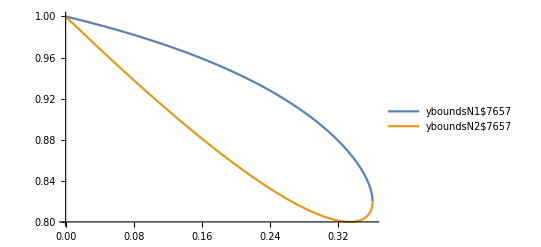

```mathematica
ybounds = getYBounds[x,0,μl*mv,μl*mv,mv]//Simplify;
xbounds=getXBounds[0,μl*mv,μl*mv,mv]//Simplify;

Module[{yboundsN1,yboundsN2,xboundsN1,xboundsN2},
(* test which curve is the upper and which is lower *)
yboundsN1=ybounds⟦1⟧/.{μl-> 0.4,mv->1};
yboundsN2=ybounds⟦2⟧/.{μl-> 0.4,mv->1};
xboundsN1=xbounds⟦1⟧/.{μl-> 0.4,mv->1};
xboundsN2=xbounds⟦2⟧/.{μl-> 0.4,mv->1};
Plot[{yboundsN1,yboundsN2},{x,xboundsN1,xboundsN2},PlotLegends->"Expressions"]
]
```

```mathematica
Module[{integral,lim1,lim2,result},
$Assumptions={xbounds⟦1⟧<x<xbounds⟦2⟧,μl>0};
integral=Integrate[vllbarγ`dΓdxdy`dynamic,y]//Simplify;
lim1=integral/.{y-> ybounds⟦1⟧};
lim2=integral/.{y-> ybounds⟦2⟧};
$Assumptions=True;
vllbarγ`dΓdx`dynamic=lim1-lim2//Simplify
]
```

1/x((x^2 (√(x-1) √(4 μl^2+x-1)-x+1))/(x-1)+(x^2 (√(x-1) √(4 μl^2+x-1)+x-1))/(x-1)+(-8 μl^4+x^2-2 (2 μl^2+1) x+2) log((x (-√(x-1) √(4 μl^2+x-1)+x-1))/(2 (x-1)))+(-8 μl^4+x^2-2 (2 μl^2+1) x+2) log((x (√(x-1) √(4 μl^2+x-1)-x+1))/(2 (x-1)))-(-8 μl^4+x^2-2 (2 μl^2+1) x+2) log(-(x (√(x-1) √(4 μl^2+x-1)+x-1))/(2 (x-1)))-(-8 μl^4+x^2-2 (2 μl^2+1) x+2) log((x (√(x-1) √(4 μl^2+x-1)+x-1))/(2 (x-1)))+(8 μl^2 (2 μl^2+1) (x-1))/(-√(x-1) √(4 μl^2+x-1)+x-1)-(8 μl^2 (2 μl^2+1) (x-1))/(√(x-1) √(4 μl^2+x-1)+x-1))

```mathematica
vllbarγ`dΓdx`dynamic//SelectNotFree[#,Log[__]]&//SelectNotFree[#,Log[__]]&//StandardForm
```

(2+x^2-8 μl^4-2 x (1+2 μl^2)) Log[(x (-1+x-√(-1+x) √(-1+x+4 μl^2)))/(2 (-1+x))]+(2+x^2-8 μl^4-2 x (1+2 μl^2)) Log[(x (1-x+√(-1+x) √(-1+x+4 μl^2)))/(2 (-1+x))]-(2+x^2-8 μl^4-2 x (1+2 μl^2)) Log[-(x (-1+x+√(-1+x) √(-1+x+4 μl^2)))/(2 (-1+x))]-(2+x^2-8 μl^4-2 x (1+2 μl^2)) Log[(x (-1+x+√(-1+x) √(-1+x+4 μl^2)))/(2 (-1+x))]

Simply logs by hand

```mathematica
+(2+x^2-8 μl^4-2 x (1+2 μl^2)) Log[(x (1-x-√(1-x) √(1-x-4 μl^2)))/(2 (1-x))]
+(2+x^2-8 μl^4-2 x (1+2 μl^2)) Log[-(x (1-x-√(1-x) √(1-x-4 μl^2)))/(2 (1-x))]
-(2+x^2-8 μl^4-2 x (1+2 μl^2)) Log[-(x (1-x+√(1-x) √(1-x-4 μl^2)))/(2 (1-x))]
-(2+x^2-8 μl^4-2 x (1+2 μl^2)) Log[(x (1-x+√(1-x) √(1-x-4 μl^2)))/(2 (1-x))]
```

```mathematica
(((x (1-x-√(1-x) √(1-x-4 μl^2)))/(2 (1-x)))/1)((-(x (1-x-√(1-x) √(1-x-4 μl^2)))/(2 (1-x)))/1)(1/(-(x (1-x+√(1-x) √(1-x-4 μl^2)))/(2 (1-x))))(1/((x (1-x+√(1-x) √(1-x-4 μl^2)))/(2 (1-x))))//Simplify//StandardForm
```

((-1+x+√(1-x) √(1-x-4 μl^2))^2)/((1-x+√(1-x) √(1-x-4 μl^2))^2)

```mathematica
vllbarγ`dΓdx`dynamic//StandardForm
```

1/x((8 (-1+x) μl^2 (1+2 μl^2))/(-1+x-√(-1+x) √(-1+x+4 μl^2))+(x^2 (1-x+√(-1+x) √(-1+x+4 μl^2)))/(-1+x)-(8 (-1+x) μl^2 (1+2 μl^2))/(-1+x+√(-1+x) √(-1+x+4 μl^2))+(x^2 (-1+x+√(-1+x) √(-1+x+4 μl^2)))/(-1+x)+(2+x^2-8 μl^4-2 x (1+2 μl^2)) Log[(x (-1+x-√(-1+x) √(-1+x+4 μl^2)))/(2 (-1+x))]+(2+x^2-8 μl^4-2 x (1+2 μl^2)) Log[(x (1-x+√(-1+x) √(-1+x+4 μl^2)))/(2 (-1+x))]-(2+x^2-8 μl^4-2 x (1+2 μl^2)) Log[-(x (-1+x+√(-1+x) √(-1+x+4 μl^2)))/(2 (-1+x))]-(2+x^2-8 μl^4-2 x (1+2 μl^2)) Log[(x (-1+x+√(-1+x) √(-1+x+4 μl^2)))/(2 (-1+x))])

Compute put logs back in

```mathematica
vllbarγ`dΓdx`dynamic=1/x((8 (-1+x) μl^2 (1+2 μl^2))/(-1+x-√(-1+x) √(-1+x+4 μl^2))+(x^2 (1-x+√(-1+x) √(-1+x+4 μl^2)))/(-1+x)-(8 (-1+x) μl^2 (1+2 μl^2))/(-1+x+√(-1+x) √(-1+x+4 μl^2))+(x^2 (-1+x+√(-1+x) √(-1+x+4 μl^2)))/(-1+x)
+(2+x^2-8 μl^4-2 x (1+2 μl^2)) Log[((-1+x+√(1-x) √(1-x-4 μl^2))^2)/((1-x+√(1-x) √(1-x-4 μl^2))^2)])//FullSimplify
```

((2 √(4 μl^2+x-1) (x^2-4 μl^2 (x-1)-2 x+2))/(√(x-1))+(-8 μl^4-4 μl^2 x+(x-2) x+2) log(((√(1-x) √(-4 μl^2-x+1)+x-1)^2)/((√(1-x) √(-4 μl^2-x+1)-x+1)^2)))/x

### Compute Spectrum

```mathematica
vllbarγ`dndx=vllbarγ`dΓdx`dynamic*vllbarγ`dΓdxdy`coeff/vllbar`Γ//FullSimplify
```

-(qe^2 ((2 √(4 μl^2+x-1) (x^2-4 μl^2 (x-1)-2 x+2))/(√(x-1))+(-8 μl^4-4 μl^2 x+(x-2) x+2) log(((√(1-x) √(-4 μl^2-x+1)+x-1)^2)/((√(1-x) √(-4 μl^2-x+1)-x+1)^2))))/(8 π^2 √(1-4 μl^2) (2 μl^2 x+x))

```mathematica
vllbarγ`dΓdx`dynamic/.{μl-> mul}//StandardForm
```

((2 √(-1+4 mul^2+x) (2-4 mul^2 (-1+x)-2 x+x^2))/(√(-1+x))+(2-8 mul^4-4 mul^2 x+(-2+x) x) Log[((-1+√(1-x) √(1-4 mul^2-x)+x)^2)/((1+√(1-x) √(1-4 mul^2-x)-x)^2)])/x

```mathematica
vllbarγ`dΓdxdy`coeff/vllbar`Γ/.{μl-> mul}//FortranForm
```

-qe**2/(8.*Sqrt(1 - 4*mul**2)*(1 + 2*mul**2)*Pi**2)

```mathematica
vllbarγ`dndx/.{μl-> 0.105,qe-> (4Pi/137.),mv-> 1.}
```

-(0.000106638 (((x-2) x-0.0441 x+1.99903) log((√(1-x) √(0.9559-x)+x-1)^2/(√(1-x) √(0.9559-x)-x+1)^2)+(2 √(x-0.9559) (x^2-2 x-0.0441 (x-1)+2))/(√(x-1))))/x

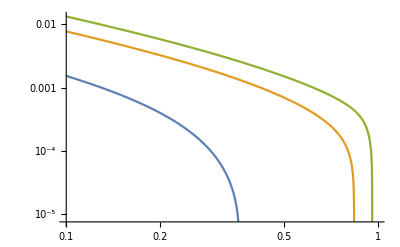

```mathematica
LogLogPlot[{vllbarγ`dndx/.{μl-> 0.4,qe-> (4Pi/137.),mv-> 1.},
vllbarγ`dndx/.{μl-> 0.2,qe-> (4Pi/137.),mv-> 1.},
vllbarγ`dndx/.{μl-> 0.1,qe-> (4Pi/137.),mv-> 1.}},{x,0.1,1}]
```